```mathematica
trikotnik =Trikotnik[{0,0}, {5,1}, {7,4}]

Stranice[Trikotnik[AA_, BB_, CC_]] := {Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}

Koti[Trikotnik[AA_, BB_, CC_]] := {Kot[CC, AA, BB],Kot[AA, BB, CC],Kot[BB, CC, AA]}

SlikaOglisc[Trikotnik[AA_, BB_, CC_]]:={Point[AA], Point[BB], Point[CC]}

SlikaStranic[Trikotnik[AA_, BB_, CC_]]:={Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}] }

NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[trikotnik]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{7,4},{0,0}]}

```mathematica
Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
SlikaOglisc[trikotnik]
```

{Point[{0,0}],Point[{5,1}],Point[{7,4}]}

```mathematica
SlikaStranic[trikotnik]
```

{Line[{{0,0},{5,1}}],Line[{{5,1},{7,4}}],Line[{{7,4},{0,0}}]}

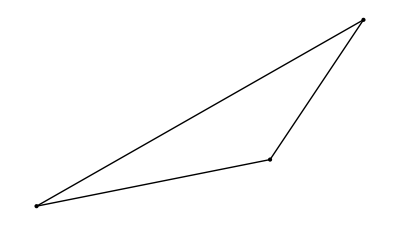

```mathematica
NarisiTrikotnik[trikotnik]
```